```mathematica
<<Wolfram`QuantumFramework`
```

This only works on a desktop with a working python session and wolframclient configured.

### Using Python session to make QiskitCircuit

You can use ResourceFunction[“SetLanguageCellSession”] to set your Python session for a LanguageCell bellow to work:

```mathematica
session=First@ExternalSessions[]
```

ExternalSessionObject[…]

```mathematica
ResourceFunction["SetLanguageCellSession"][session]
```

ExternalSessionObject[…]

If qiskit and wolframclient is pre-installed and working this should make a QiskitCircuit object:

from qiskit import QuantumRegister, ClassicalRegister, QuantumCircuit

qr = QuantumRegister(3, 'q')
anc = QuantumRegister(1, 'ancilla')
cr = ClassicalRegister(3, 'c')
qc = QuantumCircuit(qr, anc, cr)

qc.x(anc[0])
qc.h(anc[0])
qc.h(qr[0:3])
qc.cx(qr[0:3], anc[0])
qc.h(qr[0:3])
qc.barrier(qr)
qc.measure(qr, cr)

# QuantumFramework's QiskitCircuit just stores pickled QuantumCircuit

from wolframclient.language import wl
import pickle

wl.Wolfram.QuantumFramework.QiskitCircuit(pickle.dumps(qc))

QiskitCircuit[…]

```mathematica
qiskitCircuit=%;
```

```mathematica
qiskitCircuit[states]
```

```mathematica
qiskitCircuit["QuantumOperator"]
```

QuantumOperator[…]

Or use ExternalEvaluate

```mathematica
qiskitCircuit=ExternalEvaluate["Python","
from qiskit import QuantumRegister, ClassicalRegister, QuantumCircuit

qr = QuantumRegister(3, 'q')
anc = QuantumRegister(1, 'ancilla')
cr = ClassicalRegister(3, 'c')
qc = QuantumCircuit(qr, anc, cr)

qc.x(anc[0])
qc.h(anc[0])
qc.h(qr[0:3])
qc.cx(qr[0:3], anc[0])
qc.h(qr[0:3])
qc.barrier(qr)
qc.measure(qr, cr)

# QuantumFramework's QiskitCircuit just stores pickled QuantumCircuit

from wolframclient.language import wl
import pickle

wl.Wolfram.QuantumFramework.QiskitCircuit(pickle.dumps(qc))
"]
```

QiskitCircuit[…]

And then just use “QuantumCircuit” property to reconstruct QuantumCircuitOperator:

```mathematica
circuit=qiskitCircuit["QuantumCircuit"];
```

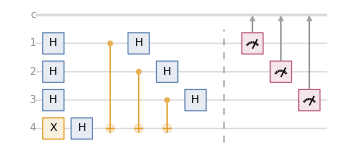

```mathematica
circuit["Diagram"]
```

```mathematica
circuit["Operators"]
```

{01+10,00/(√2)+01/(√2)+10/(√2)-11/(√2),00/(√2)+01/(√2)+10/(√2)-11/(√2),00/(√2)+01/(√2)+10/(√2)-11/(√2),00/(√2)+01/(√2)+10/(√2)-11/(√2),0000+0101+1011+1110,0000+0101+1011+1110,0000+0101+1011+1110,00/(√2)+01/(√2)+10/(√2)-11/(√2),00/(√2)+01/(√2)+10/(√2)-11/(√2),00/(√2)+01/(√2)+10/(√2)-11/(√2),000+111,000+111,000+111}

It may not support all qiskit gates properly yet, so tweaking of Qiskit.m maybe required to make your circuit convert properly:

```mathematica
SystemOpen@FileNameJoin[{
PacletObject["Wolfram/QuantumFramework"]["Location"],"Kernel","QuantumCircuitOperator","Qiskit.m"}]
```

```mathematica
QuantumMeasurementOperator[][QuantumState[]]["ReverseInput"]
```

QuantumOperator[…]

```mathematica
%["Reverse"]
```

QuantumOperator[…]

```mathematica
QuantumCircuitOperator[{"Grover",a⇒b}][]["Reverse"]
```

QuantumState[…]

```mathematica
(QuantumCircuitOperator[{"Grover",a⇒b}]/*QuantumMeasurementOperator[{1,2,3}])[]["Reverse"]
```

QuantumOperator[…]

```mathematica
QuantumMeasurement[QuantumMeasurementOperator[(QuantumCircuitOperator[{"Grover",a⇒b}]/*QuantumMeasurementOperator[{1,2,3}])[]["Reverse"]["Sort"]
]]
```

QuantumMeasurement[…]

```mathematica
(QuantumCircuitOperator[{"Grover",a⇒b}]/*QuantumMeasurementOperator[{1,2,3}])
```

QuantumCircuitOperator[…]